```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
(*pi+result*)
```

```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-up-xi1-pi-noD-S1.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgf=Interpolation[Flatten[Hdgu,1]];
Herf=Interpolation[Flatten[Heru,1]];
Hdaf=Interpolation[Flatten[Hdau,1]];
Edgf=Interpolation[Flatten[Edgu,1]];
Eerf=Interpolation[Flatten[Eeru,1]];
Edaf=Interpolation[Flatten[Edau,1]];
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-dleta-pi-xi1-S1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;
dHdau=Query[1,3]@dgpdu;
dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;
dEdau=Query[2,3]@dgpdu;

dHdaf=Interpolation[Flatten[dHdau,1]];
dEdaf=Interpolation[Flatten[dEdau,1]];
Dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-D-xi1-pi-S1.wdx"];

DHeru=Query[1,2]@Dgpdu;
DHdau=Query[1,3]@Dgpdu;

DEeru=Query[2,2]@Dgpdu;
DEdau=Query[2,3]@Dgpdu;

DHerf=Interpolation[Flatten[DHeru,1]];
DHdaf=Interpolation[Flatten[DHdau,1]];

DEerf=Interpolation[Flatten[DEeru,1]];
DEdaf=Interpolation[Flatten[DEdau,1]];
dDgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-dleta-D-pi-xi1-S1.wdx"];

dDHeru=Query[1,2]@dDgpdu;
dDHdau=Query[1,3]@dDgpdu;

dDEeru=Query[2,2]@dDgpdu;
dDEdau=Query[2,3]@dDgpdu;

dDHdaf=Interpolation[Flatten[dDHdau,1]];

dDEdaf=Interpolation[Flatten[dDEdau,1]];
```

```mathematica
(*先把上面的结果组合起来*)
```

```mathematica
Hdgall[x_,t_]:=Hdgf[x,t];
Herall[x_,t_]:=Herf[x,t]+Hdaf[x,t]+dHdaf[x,t]+DHerf[x,t]+DHdaf[x,t]+dDHdaf[x,t];
Edgall[x_,t_]:=Edgf[x,t];
Eerall[x_,t_]:=Eerf[x,t]+Edaf[x,t]+dEdaf[x,t]+DEerf[x,t]+DEdaf[x,t]+dDEdaf[x,t];
```

```mathematica
(*u quark*)
```

```mathematica
(*Σ0 k+,只需要乘上系数，u=sbar=pi+的结果*)
Coep1=(Dc-Fc)^2/(4*(0.093)^2*2*(2Pi)^4);
(*k+的u贡献，分段但就是总的*)
k1Hdg[x_,t_]=Coep1*Hdgall[x,t];
k1Her[x_,t_]=Coep1*Herall[x,t];
k1Edg[x_,t_]=Coep1*Edgall[x,t];
k1Eer[x_,t_]=Coep1*Eerall[x,t];
(*k0没有u夸克*)
(*图的u夸克总结果，就是对粒子求和*)
Hdgzall[x_,t_]=k1Hdg[x,t];
Herallwhole[x_,t_]=k1Her[x,t];
Edgzall[x_,t_]=k1Edg[x,t];
Eerallwhole[x_,t_]=k1Eer[x,t];
```

```mathematica
(*d quark*)
```

```mathematica
(*k0的d夸克，与pi0不同输入没有1/2*)
ap0=(Dc-Fc)^2/(2*2*(0.093)^2*(2Pi)^4);
(*k0的d夸克，直接就是结果没有反转*)
k0Hdg[x_,t_]=ap0*Hdgall[x,t];
k0Her[x_,t_]=ap0*Herall[x,t];
k0Edg[x_,t_]=ap0*Edgall[x,t];
k0Eer[x_,t_]=ap0*Eerall[x,t];
(*图的d夸克总结果，就是对粒子求和*)
Hdgzalld[x_,t_]=k0Hdg[x,t];
Herallwholed[x_,t_]=k0Her[x,t];
Edgzalld[x_,t_]=k0Edg[x,t];
Eerallwholed[x_,t_]=k0Eer[x,t];
```

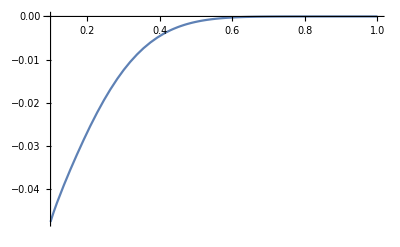

```mathematica
Plot[-I*Hdgzall[x,-1],{x,0.1,1}]
```

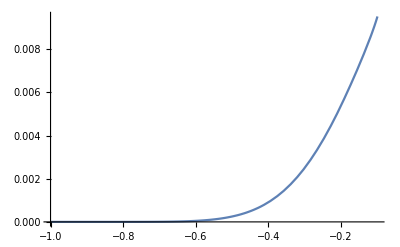

```mathematica
Plot[-I*Hdgfall[x,-1],{x,-1,-0.1}]
```

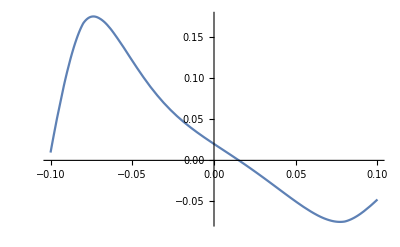

```mathematica
Plot[-I*Herallwhole[x,-1],{x,-0.1,0.1}]
```

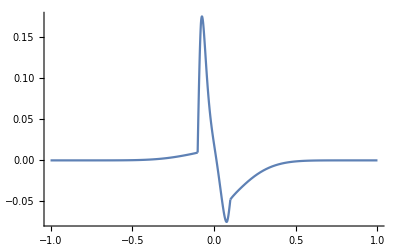

```mathematica
Show[Plot[-I*Hdgzall[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Hdgfall[x,-1],{x,-1,-0.1},PlotRange->All],Plot[-I*Herallwhole[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

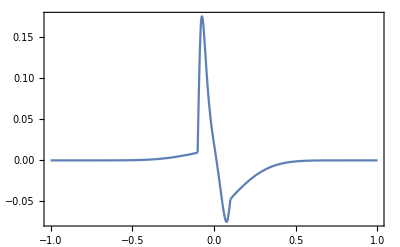
-Graphics-H_uxdiagram g

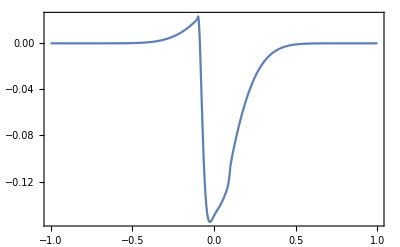
-Graphics-E_uxdiagram g

```mathematica
pHu2d=Labeled[Show[Plot[-I*Hdgzall[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Hdgfall[x,-1],{x,-1,-0.1},PlotRange->All],Plot[-I*Herallwhole[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_u","x","diagram g"},{Left,Bottom,Top},LabelStyle->24]
pEu2d=Labeled[Show[Plot[-I*Edgzall[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Edgfall[x,-1],{x,-1,-0.1},PlotRange->All],Plot[-I*Eerallwhole[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_u","x","diagram g"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
pathH=FileNameJoin[{"G:\\calc-online\\gpd\\pic\\gpd-caogao\\717",
"H-f-2d.pdf"}];
pathE=FileNameJoin[{"G:\\calc-online\\gpd\\pic\\gpd-caogao\\717",
"E-f-2d.pdf"}];
```

```mathematica
Export[pathH,pHu2d]
```

G:\calc-online\gpd\pic\gpd-caogao\717\H-f-2d.pdf

```mathematica
Export[pathE,pEu2d]
```

G:\calc-online\gpd\pic\gpd-caogao\717\E-f-2d.pdf

```mathematica
Herall[-0.07,-1]
```

0.+1.83172 ⅈ

```mathematica
Herf[-0.07,-1]
```

0.-0.150458 ⅈ

```mathematica
Hdaf[-0.07,-1]
```

0.-0.234103 ⅈ

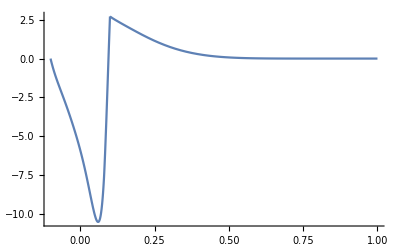

```mathematica
Show[Plot[-I*Hdgall[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

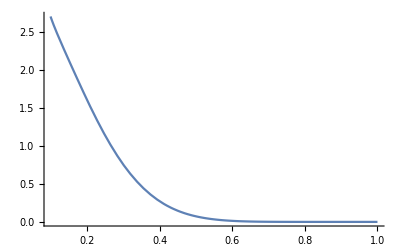

```mathematica
Plot[I*Hdgall[x,-1],{x,0.1,1},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0999959,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

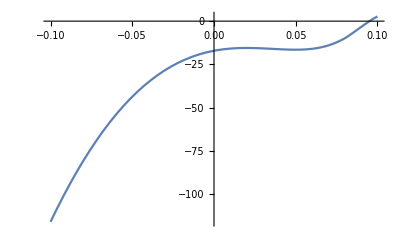

```mathematica
Plot[I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All]
```

```mathematica
p1Hdg
```

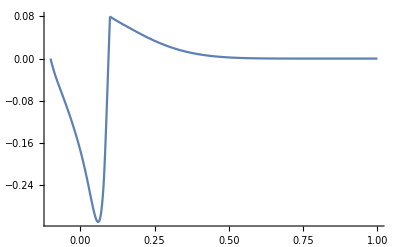

```mathematica
Show[Plot[I*p1Hdg[x,-1],{x,0.1,1},PlotRange->All],Plot[I*p1Her[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
(*s quark*)
```

```mathematica
(*k+,sbar=u，所以之后再对dbar反转得到d*)
(*pi+的dbar贡献就是u，反转*)
k1Hdgs[x_,t_]=-k1Hdg[-x,t];
k1Hers[x_,t_]=-k1Her[-x,t];
k1Edgs[x_,t_]=-k1Edg[-x,t];
k1Eers[x_,t_]=-k1Eer[-x,t];
(*k0,sbar=d*)
k0Hdgs[x_,t_]=-k0Hdg[-x,t];
k0Hers[x_,t_]=-k0Her[-x,t];
k0Edgs[x_,t_]=-k0Edg[-x,t];
k0Eers[x_,t_]=-k0Eer[-x,t];
(*图的总结果，就是对粒子求和*)
Hdgfalls[x_,t_]=k1Hdgs[x,t]+k0Hdgs[x,t];
Herallwholes[x_,t_]=k1Hers[x,t]+k0Hers[x,t];
Edgfalls[x_,t_]=k1Edgs[x,t]+k0Edgs[x,t];
Eerallwholes[x_,t_]=k1Eers[x,t]+k0Eers[x,t];
```

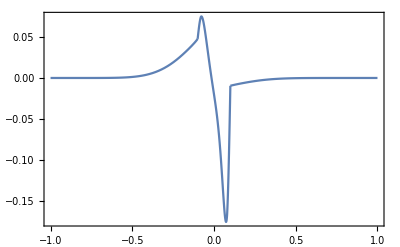
-Graphics-H_dxdiagram g

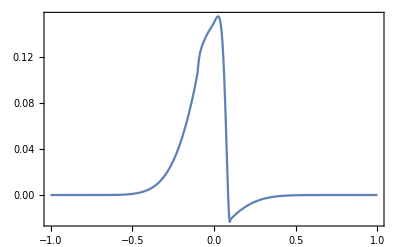
-Graphics-E_dxdiagram g

```mathematica
pHd2d=Labeled[Show[Plot[-I*Hdgzalld[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Hdgfalld[x,-1],{x,-1,-0.1},PlotRange->All],Plot[-I*Herallwholed[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d","x","diagram g"},{Left,Bottom,Top},LabelStyle->24]
pEd2d=Labeled[Show[Plot[-I*Edgzalld[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Edgfalld[x,-1],{x,-1,-0.1},PlotRange->All],Plot[-I*Eerallwholed[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d","x","diagram g"},{Left,Bottom,Top},LabelStyle->24]
```